# Lista 03 - Introdução à Física Computacional I

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.sousa@usp.br

Ao preparar o Notebook da lista, faça uso abundante de comentários e textos explicativos. Não se esqueça de rotular devidamente os eixos dos gráficos que produzir.

No mesmo espírito do mapa logístico, estude o mapa do seno, definido por: x_(n + 1) = a Sin[π x_n]

## 1.

Escolhendo a = 0.75, faça um gráfico contendo, no mesmo conjunto de eixos, a função identidade, y = x,  a função que define o mapa do seno, y = f(x) ≡ a Sin[π x_n] e a função y  = f (f(x)), todas no intervalo 0 ≤ x ≤ 1. Com base nesse gráfico, reflita se, para esse valor de a, o atrator do mapa do seno corresponde a um ponto fixo x = 0, a um ponto fixo x = x^*≠ 0 ou a um ciclo 2.

```mathematica
f[a_][x_]:=a*Sin[π x];
optam={ImageSize->Large,LabelStyle-> {"Large"}};
```

```mathematica
grafmapa[a_,x0_,n_]:=
(
xx=x0;
lista1={{xx,0},{xx,f[a][xx]}};
Do[
(
xx=f[a][xx];AppendTo[lista1,{xx,xx}];
AppendTo[lista1,{xx,f[a][xx]}]),
{i,1,n}
];
grafico0=Plot[{x,f[a][x],Nest[f[a],x,2]},{x,0,4},Evaluate[optam],AxesLabel->{"x","f(x)"}];
Show[{grafico0,ListLinePlot[lista1,PlotStyle->Red]}]
)
```

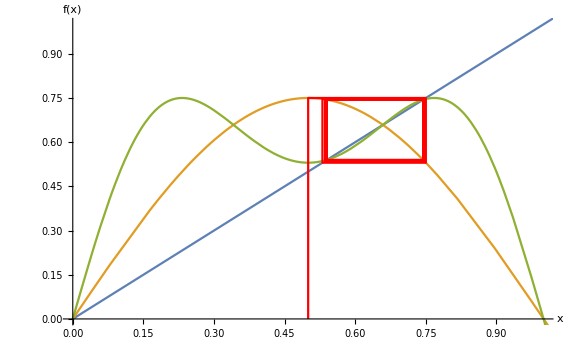

```mathematica
Show[grafmapa[0.75,0.5,10],PlotRange->{{0,1},{0,1}}]
```

(Resposta) Analisando o gráfico observamos que há uma alternância entre dos valores de x, sendo eles {0.540177, 0.744034}, com isso dizemos que há um ciclo 2.

## 2.

Produza um diagrama de bifurcações do mapa do seno utilizando 1000 valores de a entre 0 e 1. Para cada valor de a, certifique-se de haver descartado um número suficiente de aplicações do mapa para que o atrator esteja refletido fidedignamente no diagrama de bifurcações. Com base no diagrama, verifique se suas conclusões do item anterior estavam corretas. Se estiver usando o Mathematica, é melhor fazer uso de Compile quando definir a função, para garantir que o tempo de execução não seja muito longo.

```mathematica
pontos:=Compile[{a,{m,_Integer},{n,_Integer}},
(
xlista=Drop[NestList[a*Sin[π #]&,0.5,n],m+1];
saida={};
Do[AppendTo[saida,{a,xlista[[i]]}],{i,1,Length[xlista]}];
saida
),{{saida,_Real,2}}]
```

```mathematica
varrepontos:=Compile[{amin,amax,na,{m,_Integer},{n,_Integer}},
(
grandelista={};
Do[AppendTo[grandelista,pontos[a,m,n]],{a,amin,amax,(amax-amin)/na}];
Flatten[grandelista,1]
),{{grandelista,_Real,3}}]
```

```mathematica
diagbifurca[amin_,amax_,na_,m_,n_]:=ListPlot[varrepontos[amin,amax,na,m,n],Axes->False,Frame->True,FrameLabel->{"a","x"},PlotStyle->PointSize[0.001],AspectRatio->1,Evaluate[optam]]
```

```mathematica
diagbifurca[0,1,1000,1024,2048]
```

-Graphics-

## 3.

Determine, com precisão de máquina, os menores valores de a entre 0 e 1 que tornam instáveis os ciclos com período n entre 2 e 128.  Pode ser útil traçar ampliações dos diagramas de bifurcação de modo a encontrar palpites adequados para os valores de a.

A primeira bifurcação acontece nos pontos {0.7148451021114569, 0.6456078632836839}, obtidos pelo cursor do Mathematica. Assim, faremos o diagrama de bifurcação indo de 0.72 à 1.

```mathematica
Show[diagbifurca[0.72,1,1000,1024,2048]
```

## 4.

A partir de uma tabela construída com os resultados do item anterior, obtenha estimativas para a constante δ de Feigenbaum utilizando as bifurcações que marcam a instabilidade dos ciclos de período 2^(j - 1), 2^j e 2^(j + 1). Se a_(j - 1), a_j e a_(j + 1) são os valores de a nessas bifurcações, a estimativa correspondente para a constante de Feigenbaum é δ_j = (a_j - a_(j - 1))(a_(j + 1) - a_j). Suas estimativas sucessivas parecem tender ao valor exato (com 10 algarismos significativos) para o mapa logístico, δ_log = 4.669201609?

## 5.

Seja Δ_j a diferença entre δ_log e suas estimativas δ_j, com j entre 3 e 7. Procure um ajuste para Δ_j da forma C_1 Exp[- C_2j]  e trace os dados e o ajuste no mesmo conjunto de eixos, com as abscissas em escala linear e as ordenadas em escala logarítmica. O que o gráfico sugere a respeito do comportamento de δ_j quando j ≫ 1?

## 6.

Finalmente, determine com 3 algarismos significativos o valor do expoente de Lyapunov para o mapa do seno quando a = 1 e faça um gráfico desse expoente para a entre 0.5 e 1. Quais são as regiões em que o mapa exibe comportamento caótico?